## Analysis of the unreduced in-patch model

#### This document includes:

The code used for Appendix B

## ODEs

```mathematica
Clear[GenerateSidModel];
GenerateSidModel[N_]:=(
Flatten[{
(* biomass: growth - washout *)
Table[M[i]'[t]==Growth[α[i],Holo[t]]*M[i][t]-d*M[i][t]
,{i,1,N}],
(* Apo: production + recycling - chelation - washout  *)
Apo'[t]==sApo+Sum[M[j][t]*(α[j]*ϵ+HoloFlux[Holo[t]]*ρ),{j,N}]
-Chelation[Apo[t],Fe[t]]-d*Apo[t],
(* Holo: chelation - uptake - washout  *)
Holo'[t]==Chelation[Apo[t],Fe[t]]-HoloFlux[Holo[t]]*(Sum[M[j][t],{j,N}])-d*Holo[t],
(* Fe: supply - chelation - private - washout *)
Fe'[t]==sFe-Chelation[Apo[t],Fe[t]]-d*Fe[t]
}]
);

Clear[Chelation,HoloFlux, Growth];
Chelation[apo_,fe_]:=kf*apo*fe;
HoloFlux[holo_]:= vh*holo/(Kh+holo);
Growth[alpha_, holo_]:=(1-alpha)*γ*HoloFlux[holo];
```

## Solutions for one strain

```mathematica
odes=GenerateSidModel[1];
Column[odes]
eqs=Map[0==Last[#]&,odes]/.Map[#[t]->#&,{M[1],Apo,Holo,Fe}];
Column[eqs]
```

M[1]'[t]==-d M[1][t]+(vh γ Holo[t] (1-α[1]) M[1][t])/(Kh+Holo[t])
Apo'[t]==sApo-d Apo[t]-kf Apo[t] Fe[t]+((vh ρ Holo[t])/(Kh+Holo[t])+ϵ α[1]) M[1][t]
Holo'[t]==kf Apo[t] Fe[t]-d Holo[t]-(vh Holo[t] M[1][t])/(Kh+Holo[t])
Fe'[t]==sFe-d Fe[t]-kf Apo[t] Fe[t]

0==-d M[1]+(Holo vh γ M[1] (1-α[1]))/(Holo+Kh)
0==-Apo d-Apo Fe kf+sApo+M[1] ((Holo vh ρ)/(Holo+Kh)+ϵ α[1])
0==-d Holo+Apo Fe kf-(Holo vh M[1])/(Holo+Kh)
0==-d Fe-Apo Fe kf+sFe

### Trivial solution: no biomass

```mathematica
extinction=Solve[Simplify[eqs/.M[1]->0],{Apo,Holo,Fe},NonNegativeReals,
Assumptions->{0<=α[1]<=1,0<=ρ<=1,Map[#>0&,{vh,γ,Kh,ϵ,d,sFe,kf,sApo}]}]
```

{{Apo→sApo/(d+kf ((-d^2-kf sApo+kf sFe)/(2 d kf)+(√(d^4+2 d^2 kf sApo+kf^2 sApo^2+2 d^2 kf sFe-2 kf^2 sApo sFe+kf^2 sFe^2))/(2 d kf))),Holo→(kf sApo ((-d^2-kf sApo+kf sFe)/(2 d kf)+(√(d^4+2 d^2 kf sApo+kf^2 sApo^2+2 d^2 kf sFe-2 kf^2 sApo sFe+kf^2 sFe^2))/(2 d kf)))/(d (d+kf ((-d^2-kf sApo+kf sFe)/(2 d kf)+(√(d^4+2 d^2 kf sApo+kf^2 sApo^2+2 d^2 kf sFe-2 kf^2 sApo sFe+kf^2 sFe^2))/(2 d kf)))),Fe→(-d^2-kf sApo+kf sFe)/(2 d kf)+(√(d^4+2 d^2 kf sApo+kf^2 sApo^2+2 d^2 kf sFe-2 kf^2 sApo sFe+kf^2 sFe^2))/(2 d kf)}}

```mathematica
FullSimplify[extinction]
```

{{Apo→(2 d sApo)/(d^2-kf sApo+kf sFe+√(d^4+kf^2 (sApo-sFe)^2+2 d^2 kf (sApo+sFe))),Holo→(d^2+kf (sApo+sFe)-√(d^4+kf^2 (sApo-sFe)^2+2 d^2 kf (sApo+sFe)))/(2 d kf),Fe→(-d^2-kf sApo+kf sFe+√(d^4+kf^2 (sApo-sFe)^2+2 d^2 kf (sApo+sFe)))/(2 d kf)}}

```mathematica
extinction=Solve[Simplify[eqs/.M[1]->0/.sApo->0],{Apo,Holo,Fe},NonNegativeReals,
Assumptions->{0<=α[1]<=1,0<=ρ<=1,Map[#>0&,{vh,γ,Kh,ϵ,d,sFe,kf,sApo}]}]
```

{{Apo→0,Holo→0,Fe→sFe/d}}

#### Find the Jacobian matrix to determine stability

```mathematica
rhs=Map[Last,eqs]
```

{-d M[1]+(Holo vh γ M[1] (1-α[1]))/(Holo+Kh),-Apo d-Apo Fe kf+sApo+M[1] ((Holo vh ρ)/(Holo+Kh)+ϵ α[1]),-d Holo+Apo Fe kf-(Holo vh M[1])/(Holo+Kh),-d Fe-Apo Fe kf+sFe}

```mathematica
jac={D[rhs,M[1]],D[rhs,Apo],D[rhs,Holo],D[rhs,Fe]};

Simplify[jac]//MatrixForm
```

(-d-(Holo vh γ (-1+α[1]))/(Holo+Kh) | (Holo vh ρ)/(Holo+Kh)+ϵ α[1] | -(Holo vh)/(Holo+Kh) | 0
0 | -d-Fe kf | Fe kf | -Fe kf
-(Kh vh γ M[1] (-1+α[1]))/(Holo+Kh)^2 | (Kh vh ρ M[1])/(Holo+Kh)^2 | -(d (Holo+Kh)^2+Kh vh M[1])/(Holo+Kh)^2 | 0
0 | -Apo kf | Apo kf | -d-Apo kf)

Evaluate the Jacobian at the extinction equilibrium

```mathematica
jac/.{M[1]->0,Apo->0,Holo->0,Fe->sFe/d}//MatrixForm
```

(-d | ϵ α[1] | 0 | 0
0 | -d-(kf sFe)/d | (kf sFe)/d | -(kf sFe)/d
0 | 0 | -d | 0
0 | 0 | 0 | -d)

```mathematica
Eigenvalues[jac/.{M[1]->0,Apo->0,Holo->0,Fe->sFe/d}]
```

{-d,-d,-d,(-d^2-kf sFe)/d}

The eigenvalues are always negative, so this solution is always stable.

### Additional real, positive solutions

Takes a few minutes on my computer

```mathematica
sols=Solve[eqs,{M[1],Apo,Holo,Fe},NonNegativeReals,
Assumptions->Flatten[{0<α[1]<1,0<=ρ<=1,Map[#>0&,{vh,γ,Kh,ϵ,d,sFe,kf}]}]];
```

```mathematica
sols
```

```mathematica
Length[sols]
```

3

Do conditions for the non-zero solutions match, i.e. they form a pair?

```mathematica
conds=sols[[2]][[1]][[2]][[2]]
conds2=sols[[3]][[1]][[2]][[2]]
```

γ>(-d+d ρ)/(-ϵ α[1]+ϵ α[1]^2)&&kf>d^3/(-d sFe+d sFe ρ+sFe γ ϵ α[1]-sFe γ ϵ α[1]^2)&&vh>-d/(-γ+γ α[1])&&Kh<1/(d^2 kf (d ρ+γ ϵ α[1]-γ ϵ α[1]^2))(-d^4+d^2 kf sFe+d^3 vh γ-d kf sFe vh γ-d^2 kf sFe ρ+d kf sFe vh γ ρ-d^3 vh γ α[1]+d kf sFe vh γ α[1]-d kf sFe γ ϵ α[1]+kf sFe vh γ^2 ϵ α[1]-d kf sFe vh γ ρ α[1]+d kf sFe γ ϵ α[1]^2-2 kf sFe vh γ^2 ϵ α[1]^2+kf sFe vh γ^2 ϵ α[1]^3)-1/Abs[d ρ+γ ϵ α[1]-γ ϵ α[1]^2]2 √(1/(d kf)) √(-d^3 sFe+2 d^2 sFe vh γ-d sFe vh^2 γ^2+d^3 sFe ρ-2 d^2 sFe vh γ ρ+d sFe vh^2 γ^2 ρ-2 d^2 sFe vh γ α[1]+2 d sFe vh^2 γ^2 α[1]+d^2 sFe γ ϵ α[1]-2 d sFe vh γ^2 ϵ α[1]+sFe vh^2 γ^3 ϵ α[1]+2 d^2 sFe vh γ ρ α[1]-2 d sFe vh^2 γ^2 ρ α[1]-d sFe vh^2 γ^2 α[1]^2-d^2 sFe γ ϵ α[1]^2+4 d sFe vh γ^2 ϵ α[1]^2-3 sFe vh^2 γ^3 ϵ α[1]^2+d sFe vh^2 γ^2 ρ α[1]^2-2 d sFe vh γ^2 ϵ α[1]^3+3 sFe vh^2 γ^3 ϵ α[1]^3-sFe vh^2 γ^3 ϵ α[1]^4)

γ>(-d+d ρ)/(-ϵ α[1]+ϵ α[1]^2)&&kf>d^3/(-d sFe+d sFe ρ+sFe γ ϵ α[1]-sFe γ ϵ α[1]^2)&&vh>-d/(-γ+γ α[1])&&Kh<1/(d^2 kf (d ρ+γ ϵ α[1]-γ ϵ α[1]^2))(-d^4+d^2 kf sFe+d^3 vh γ-d kf sFe vh γ-d^2 kf sFe ρ+d kf sFe vh γ ρ-d^3 vh γ α[1]+d kf sFe vh γ α[1]-d kf sFe γ ϵ α[1]+kf sFe vh γ^2 ϵ α[1]-d kf sFe vh γ ρ α[1]+d kf sFe γ ϵ α[1]^2-2 kf sFe vh γ^2 ϵ α[1]^2+kf sFe vh γ^2 ϵ α[1]^3)-1/Abs[d ρ+γ ϵ α[1]-γ ϵ α[1]^2]2 √(1/(d kf)) √(-d^3 sFe+2 d^2 sFe vh γ-d sFe vh^2 γ^2+d^3 sFe ρ-2 d^2 sFe vh γ ρ+d sFe vh^2 γ^2 ρ-2 d^2 sFe vh γ α[1]+2 d sFe vh^2 γ^2 α[1]+d^2 sFe γ ϵ α[1]-2 d sFe vh γ^2 ϵ α[1]+sFe vh^2 γ^3 ϵ α[1]+2 d^2 sFe vh γ ρ α[1]-2 d sFe vh^2 γ^2 ρ α[1]-d sFe vh^2 γ^2 α[1]^2-d^2 sFe γ ϵ α[1]^2+4 d sFe vh γ^2 ϵ α[1]^2-3 sFe vh^2 γ^3 ϵ α[1]^2+d sFe vh^2 γ^2 ρ α[1]^2-2 d sFe vh γ^2 ϵ α[1]^3+3 sFe vh^2 γ^3 ϵ α[1]^3-sFe vh^2 γ^3 ϵ α[1]^4)

```mathematica
conds===conds2
```

True

#### α cannot be 0 or 1

Can be seen in this part of the condition for the non-zero solutions:

```mathematica
cond =γ>(-d+d ρ)/(-ϵ α[1]+ϵ α[1]^2)
```

γ>(-d+d ρ)/(-ϵ α[1]+ϵ α[1]^2)

```mathematica
cond/.α[1]->0
```

Power::infy: Infinite expression 1/0 encountered.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

γ>ComplexInfinity

```mathematica
cond/.α[1]->1
```

Power::infy: Infinite expression 1/0 encountered.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

γ>ComplexInfinity

### Stability of the non-trivial solutions

The Jacobian was too complicated to analytically determine the stability.

## Numeric solution

```mathematica
Clear[defaults];
defaults={
(* Chemostat stuff *)
sFe->1,
d->1,

kf->1,
γ->10.,
vh->1,Kh->0.1,
ϵ->2.,
ρ->1.
};
```

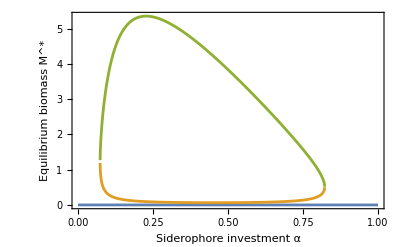

```mathematica
Plot[Evaluate[M[1]/.(sols/.defaults)],{α[1],0,1},
Frame->True,FrameLabel->{"Siderophore investment α","Equilibrium biomass M^*"},
PlotTheme->"Default",BaseStyle->Directive[FontSize->13,FontColor->Black],LabelStyle->Directive[FontSize->11,FontColor->Black]
]
```

### Bifurcation points: α_min and α_max

```mathematica
Reduce[conds/.defaults,α[1]]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

0.0738069<α[1]<0.822162

```mathematica
limits =%
```

0.0738069<α[1]<0.822162

### Stability of the solutions for these parameters

```mathematica
numSols=FullSimplify[sols/.defaults, Assumptions->limits];
```

The eigenvalues of the Jacobian are still too complicated to compute. Best we can do is compute stability of each solution for various α

```mathematica
(* Test if the real parts of the Jacobian eigenvalues are negative (= stabile) *)
AllTrue[Table[Map[AllTrue[Re[Eigenvalues[jac/.defaults/.#/.α[1]->0.1]],Negative]&,numSols]
, {α[1],0.074,0.822, 0.001}], #=={True,False,True}&]
```

True

The three solutions are consistently {Stable, Unstable, Stable} between α_min and α_max.

```mathematica
numSols/.defaults/.α[1]->0.2
```

{{M[1]→0,Apo→0,Holo→0,Fe→1},{M[1]→0.106751,Apo→0.0284147,Holo→0.0142857,Fe→0.97237},{M[1]→5.31468,Apo→2.11159,Holo→0.0142857,Fe→0.32138}}

Solution 3 is the positive equilibrium

### Value of α that maximizes biomass (α̂)

```mathematica
NMaximize[{M[1]/.numSols[[3]], limits}, α[1]]
```

{5.35138,{α[1]→0.226797}}

α̂ is approximately 0.227

### Bifurcation diagram (Figure 2B)

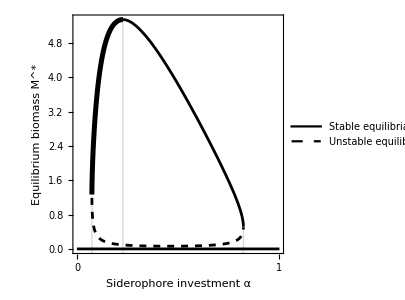

```mathematica
lines=Evaluate[M[1]/.(sols/.defaults)];
(* Split function so it can be colored differently *) 
stable=lines[[3]];
lines[[3]]=ConditionalExpression[stable,α[1]>0.227];
AppendTo[lines, ConditionalExpression[stable,α[1]<0.227]];
pltvsalpha=Plot[lines,{α[1],0,1},
PlotStyle->{Black,{Black,Dashed},Black, {Black,Thickness[0.012]}},
Frame->True,FrameLabel->{"Siderophore investment α","Equilibrium biomass M^*"},
PlotTheme->"Default",BaseStyle->Directive[FontSize->13,FontColor->Black],LabelStyle->Directive[FontSize->11,FontColor->Black],
PlotLegends->Placed[LineLegend[{Black,{Black,Dashed}},{"Stable equilibria", "Unstable equilibrium"},LegendMarkerSize->{22,10}],{Right,Top}],
PlotRangeClipping->False,
FrameTicks->{{Automatic,None},{{0,1},None}},
Prolog->{
Directive[LightGray],
Line[{{0.073807,-0.35},{0.073807,1.224779191545329}}],
Line[{{0.2268,-0.35},{0.2268,5.351}}],
Line[{{0.822162, -0.35},{0.822162, 0.509}}],
Black,FontSize->11,
Text["α_min",{0.073807,-0.51}],
Text["α̂",{0.2268,-0.51}],
Text["α_max",{0.822162,-0.51}]
},
ImageSize->300,AspectRatio->1
]
```

### Bifurcation diagrams for all state variables (Fig. S2)

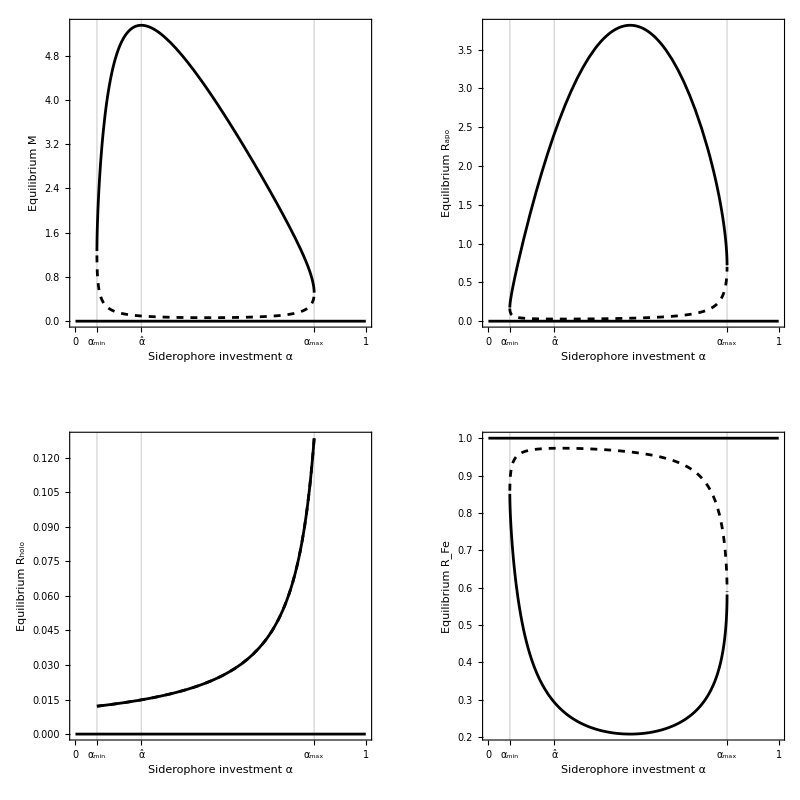

```mathematica
GraphicsGrid[Partition[Table[(
lines=Evaluate[var/.(sols/.defaults)];
pltvsalpha=Plot[lines,{α[1],0,1},
PlotRange->All,
PlotStyle->{Black,{Black,Dashed},Black, {Black,Thickness[0.012]}},
Frame->True,FrameLabel->{"Siderophore investment α","Equilibrium " <> (var/.{{M[1]->"M",Apo->"R_apo",Holo->"R_holo",Fe->"R_Fe"}})},
PlotTheme->"Default",BaseStyle->Directive[FontSize->13,FontColor->Black],LabelStyle->Directive[FontSize->11,FontColor->Black],
FrameTicks->{{Automatic,None},{{0, {0.073807,"α_min"}, {0.2268,"α̂"},  {0.822162, "α_max"},1},None}},
Prolog->{
Directive[LightGray],
Line[{{0.073807,-0.35},{0.073807,10}}],
Line[{{0.2268,-0.35},{0.2268,10}}],
Line[{{0.822162, -0.35},{0.822162,10}}]
},
ImageSize->300,AspectRatio->1
]
),
{var, {M[1],Apo,Holo,Fe}}],2]]
```

### Competitive ability with the R* rule (Figure 2C)

Growth depends on R_holo - strain with the lowest equilibrium value will replace all others

```mathematica
Rholo[a_]:=d*Kh/(vh*γ*(1-a)-d)/.defaults;
```

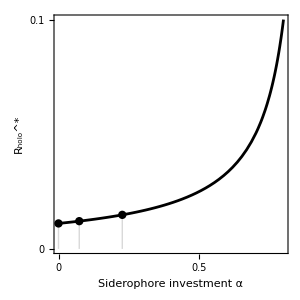

```mathematica
plotRstar=Plot[Rholo[a],{a,0,0.8}, PlotRange->{0,0.1},
PlotStyle->Black,
Frame->True,FrameLabel->{"Siderophore investment α","R_holo^*"},
BaseStyle->Directive[FontSize->13,FontColor->Black],LabelStyle->Directive[FontSize->13,FontColor->Black],
FrameTicks->{{{0,0.1},None},{{0,0.5},None}},
ImageSize->300,AspectRatio->1,
PlotRangeClipping->False,
Prolog->{
Directive[LightGray],
Line[{{0,0},{0,Rholo[0]}}],
Line[{{0.073807,0},{0.073807,Rholo[0.073807]}}],
Line[{{0.2268,0},{0.2268,Rholo[0.2268]}}],
Black,FontSize->12,
Text["α_min",{0.073807,-0.0038}],
Text["α̂",{0.2268,-0.0038}],
PointSize[0.02],
Point[{0,Rholo[0]}],
Point[{0.073807,Rholo[0.073807]}],
Point[{0.2268,Rholo[0.2268]}]
}
]
```

### CC tradeoff (Figure 4)

```mathematica
Mstar[a_]:=M[1]/.(sols[[3]]/.defaults)/.α[1]->a;
```

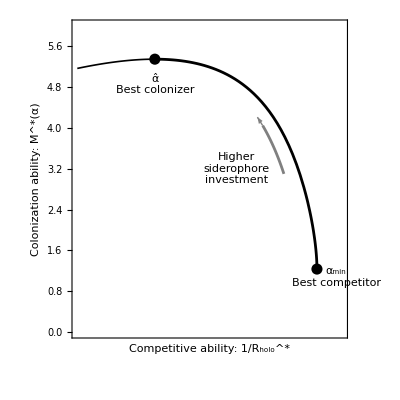

```mathematica
pltCC=Show[ParametricPlot[Evaluate@{1/Rholo[a],Mstar[a]},{a,0.05,0.227}, (* frontier *)
PlotStyle->Black,
PlotRange->{{60,85},{0,6}},
Frame->True,FrameLabel->{"Competitive ability: 1/R_holo^*","Colonization ability: M^*(α)"},
FrameTicks->{None,Automatic},
PlotTheme->"Default",BaseStyle->Directive[FontSize->13,FontColor->Black],
LabelStyle->Directive[FontSize->13,FontColor->Black],AspectRatio->1,
Epilog->{
Directive[PointSize[0.02]],
Point[{1/Rholo[a],Mstar[a]}/.a->0.073807],
Text["α_min\nBest competitor",{1/Rholo[a]+1.8,Mstar[a]-0.15}/.a->0.073807,{1,0}],
Point[{1/Rholo[a],Mstar[a]}/.a->0.2268],
Text["α̂\nBest colonizer",{1/Rholo[a],Mstar[a]-0.5}/.a->0.2268],
Directive[Gray],
Arrow[{{1/Rholo[a]-1.5,Mstar[a]}/.(a->0.11), {1/Rholo[a]-1.5,Mstar[a]}/.(a->0.115)}],
Directive[Black,FontSize->11],
Text["Higher\nsiderophore\ninvestment",{75,3.2}]
},
ImageSize->{300}
],
ParametricPlot[Evaluate@{1/Rholo[a],Mstar[a]},{a,0.227,0.3},PlotStyle->{Black,Thickness[0.003]}],
ParametricPlot[Evaluate@{1/Rholo[a]-1.5,Mstar[a]},{a,0.09,0.11},PlotStyle->Gray] (* arrow*)
]
```

## Representative Dynamics (Figure 1A and D)

```mathematica
Clear[SolvePatch];
SolvePatch[alphas_,start_:1,params_:{},maxT_:1000,stop_:True]:=Module[
{
size=Length[alphas],
starts,
odes,
stateVars,
conditions,
method,
endT=maxT,
sol
},
Clear[M,Apo,Holo,Fe,t,α,apoStart,holoStart,feStart];
starts=If[NumericQ[start],ConstantArray[start,size],start];
If[size!=Length[starts],Print["Vectors are of unequal size!"];Abort[]];
odes=GenerateSidModel[size];
stateVars=Flatten[{Array[M,size],Apo,Holo,Fe}];
conditions=Join[params,defaults];
method=If[stop,
{"EventLocator",
"Event"->Total[Abs[Map[First,odes]]]>10^-6,
"EventAction":>Throw[endT= t,"StopIntegration"]},
Automatic];
sol=NDSolve[{
odes,
Thread[Array[M[#][0]&,size]==starts],
Apo[0]==apoStart,Holo[0]==holoStart,Fe[0]==feStart
}//.conditions//.Thread[Array[α,size]->alphas],
stateVars,{t,0,maxT},
Method->method
];
Association[Append[sol[[1]],"end"->endT]]
];
```

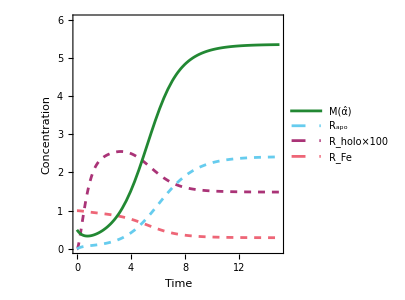

```mathematica
sol1=SolvePatch[{0.227,0.074,0},{0.5,0,0},
{apoStart->0,holoStart->0,feStart->sFe},
50,False];

legend=Reverse[{"M(α̂)","R_apo",Row[{"R_holo",Style["×100",11]}], "R_Fe"}];
Plot[Evaluate[Reverse[{M[1][t],Apo[t],Holo[t]*100,Fe[t]}]/.sol1],{t,0,Min[sol1["end"],15]},
PlotRange->{0,6},
PlotLegends->Placed[LineLegend[
legend,LegendLayout->"ReversedColumn",
LegendMarkerSize->{22,5}],
{0.2,0.8}],
Frame->True,FrameLabel->{"Time","Concentration"},
PlotStyle->Reverse[{RGBColor["#228833"],{Dashed,RGBColor["#66CCEE"]},{Dashed,RGBColor["#AA3377"]},{Dashed,RGBColor["#EE6677"]}}],
BaseStyle->Directive[FontSize->14,FontColor->Black],LabelStyle->Directive[FontSize->14,FontColor->Black],
ImageSize->300,AspectRatio->1
]
```

```mathematica
Map[#[sol1["end"]]&,sol1]
```

<|M[1]→5.35138,M[2]→0.,M[3]→0.,Apo→2.41467,Holo→0.0148588,Fe→0.292854,end→50[50]|>

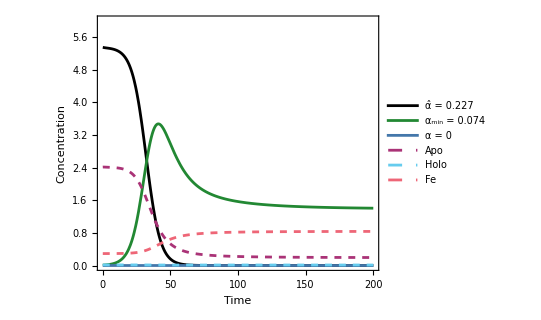

```mathematica
sol2=SolvePatch[{0.227,0.074,0},{5.351375992155946,0.01,0},
{apoStart->2.4146653412953865,holoStart->0.014858842372431819,feStart->0.29285448335132197}];

legend={"α̂ = 0.227","α_min = 0.074","α = 0","Apo","Holo","Fe"};
Plot[Evaluate[{M[1][t],M[2][t],M[3][t],Apo[t],Holo[t],Fe[t]}/.sol2],{t,0,Min[sol2["end"],200]},
PlotRange->{0,6},PlotLegends->legend,
Frame->True,FrameLabel->{"Time","Concentration"},
PlotStyle->{Black,RGBColor["#228833"],RGBColor["#4477AA"],{Dashed,RGBColor["#AA3377"]},{Dashed,RGBColor["#66CCEE"]},{Dashed,RGBColor["#EE6677"]}},
BaseStyle->Directive[FontSize->14,FontColor->Black],LabelStyle->Directive[FontSize->18,FontColor->Black],
AspectRatio->0.8
]
```

```mathematica
Map[#[150]&,sol2]
```

<|M[1]→5.82766×10^-9,M[2]→1.43879,M[3]→0.,Apo→0.201016,Holo→0.0120959,Fe→0.832527,end→513.651[150]|>

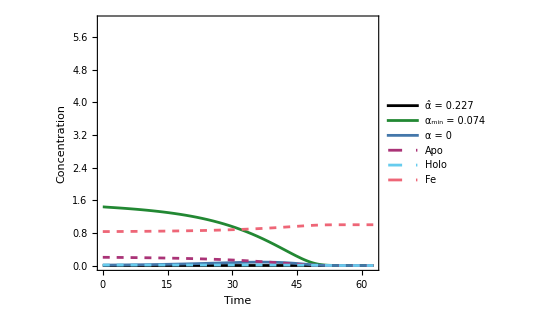

```mathematica
sol3=SolvePatch[{0.227,0.074,0},{0,1.438790639201347,0.01},
{apoStart->0.20101624196832285,holoStart->0.012095911532721514,feStart->0.832527128836341}];

legend={"α̂ = 0.227","α_min = 0.074","α = 0","Apo","Holo","Fe"};
Plot[Evaluate[{M[1][t],M[2][t],M[3][t],Apo[t],Holo[t],Fe[t]}/.sol3],{t,0,Min[sol3["end"],200]},
PlotRange->{0,6},PlotLegends->legend,
Frame->True,FrameLabel->{"Time","Concentration"},
PlotStyle->{Black,RGBColor["#228833"],RGBColor["#4477AA"],{Dashed,RGBColor["#AA3377"]},{Dashed,RGBColor["#66CCEE"]},{Dashed,RGBColor["#EE6677"]}},
BaseStyle->Directive[FontSize->14,FontColor->Black],LabelStyle->Directive[FontSize->18,FontColor->Black],
AspectRatio->0.8
]
```

```mathematica
vars={Holo,Apo,Fe,M[1],M[2],M[3]};
t1=0; t2=t1+150; tend=t2+65;
combo[t]=Table[Piecewise[{
{var[50]/.{M[2]->None,M[3]->None}/.sol1,t<=t1},
{var[t-t1]/.{M[3]->None}/.sol2,t1<t<=t2},
{var[t-t2]/.sol3,t2<t}
}],{var,vars}];
```

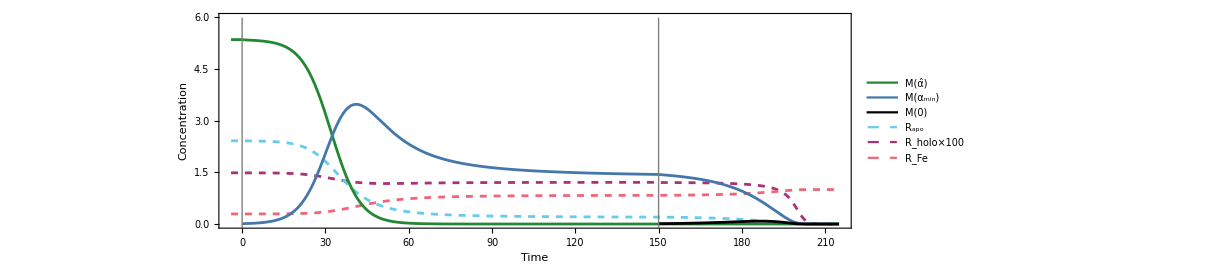

```mathematica
legend={"M(α̂)","M(α_min)","M(0)","R_apo",Row[{"R_holo",Style["×100",11]}],"R_Fe"};
colors={{Dashed,RGBColor["#AA3377"]},{Dashed,RGBColor["#66CCEE"]},{Dashed,RGBColor["#EE6677"]},RGBColor["#228833"],RGBColor["#4477AA"],Black};
pltDyn=Plot[Evaluate@ReplacePart[combo[t],1->combo[t][[1]]*100],{t,-4,tend},
PlotRange->{0,5.99},PlotRangePadding->{{0,-3},{0,0}},
PlotLegends->Placed[LineLegend[
colors[[{4,5,6,2,1,3}]],legend,LegendLayout->{"Column",2},LegendMarkerSize->{25,10}],
{0.55,Top}],
Frame->True,FrameLabel->{"Time","Concentration"},FrameTicks->{{Automatic,None},{Automatic,None}},
PlotStyle->colors,
BaseStyle->Directive[FontSize->14,FontColor->Black],LabelStyle->Directive[FontSize->13,FontColor->Black],
Prolog->{
(*Opacity[0],EdgeForm[{Gray,Thickness[0.003]}],Rectangle[{t2,0},{tend,0.15}]*)
},
Epilog->{
Black,FontSize->13,
Inset[
Plot[Evaluate@ReplacePart[combo[t],1->combo[t][[1]]*100],{t,t2-2.5,tend-5},
PlotRange->{All,{0,0.12}},PlotStyle->colors,Frame->True,
FrameTicks->{{{0.05,0.1,0.15},None},{{160,180,200},None}},
Background->White,Exclusions->t2,ImageSize->273, PlotRangePadding->0],
{142,5.8},{Left,Top}],
Gray,Line[{{t1,-0.1},{t1,5.99}}],Line[{{t2,-0.1},{t2,5.99}}],
Black,FontSize->11
},
ImageSize->{900,300},AspectRatio->0.3
]
```

## Parameter sweeps (Figure S3)

```mathematica
tolIridescent = Map[RGBColor,{"#FEFBE9","#FCF7D5","#F5F3C1","#EAF0B5","#DDECBF","#D0E7CA","#C2E3D2","#B5DDD8","#A8D8DC","#9BD2E1","#8DCBE4","#81C4E7","#7BBCE7","#7EB2E4","#88A5DD","#9398D2","#9B8AC4","#9D7DB2","#9A709E","#906388","#805770","#684957","#46353A"}]
```

{RGBColor[0.996078431372549, 0.984313725490196, 0.9137254901960784],RGBColor[0.9882352941176471, 0.9686274509803922, 0.8352941176470589],RGBColor[0.9607843137254902, 0.9529411764705882, 0.7568627450980392],RGBColor[0.9176470588235294, 0.9411764705882353, 0.7098039215686275],RGBColor[0.8666666666666667, 0.9254901960784314, 0.7490196078431373],RGBColor[0.8156862745098039, 0.9058823529411765, 0.792156862745098],RGBColor[0.7607843137254902, 0.8901960784313725, 0.8235294117647058],RGBColor[0.7098039215686275, 0.8666666666666667, 0.8470588235294118],RGBColor[0.6588235294117647, 0.8470588235294118, 0.8627450980392157],RGBColor[0.6078431372549019, 0.8235294117647058, 0.8823529411764706],RGBColor[0.5529411764705883, 0.796078431372549, 0.8941176470588236],RGBColor[0.5058823529411764, 0.7686274509803922, 0.9058823529411765],RGBColor[0.4823529411764706, 0.7372549019607844, 0.9058823529411765],RGBColor[0.49411764705882355, 0.6980392156862745, 0.8941176470588236],RGBColor[0.5333333333333333, 0.6470588235294118, 0.8666666666666667],RGBColor[0.5764705882352941, 0.596078431372549, 0.8235294117647058],RGBColor[0.6078431372549019, 0.5411764705882353, 0.7686274509803922],RGBColor[0.615686274509804, 0.49019607843137253, 0.6980392156862745],RGBColor[0.6039215686274509, 0.4392156862745098, 0.6196078431372549],RGBColor[0.5647058823529412, 0.38823529411764707, 0.5333333333333333],RGBColor[0.5019607843137255, 0.3411764705882353, 0.4392156862745098],RGBColor[0.40784313725490196, 0.28627450980392155, 0.3411764705882353],RGBColor[0.27450980392156865, 0.20784313725490197, 0.22745098039215686]}

```mathematica
colors=tolIridescent[[{10,13,16,19,22}]];
styles=Flatten[Outer[List,colors,{Dashed,Automatic}],{1,2}]
```

{{RGBColor[0.6078431372549019, 0.8235294117647058, 0.8823529411764706],Dashing[{Small,Small}]},{RGBColor[0.6078431372549019, 0.8235294117647058, 0.8823529411764706],Automatic},{RGBColor[0.4823529411764706, 0.7372549019607844, 0.9058823529411765],Dashing[{Small,Small}]},{RGBColor[0.4823529411764706, 0.7372549019607844, 0.9058823529411765],Automatic},{RGBColor[0.5764705882352941, 0.596078431372549, 0.8235294117647058],Dashing[{Small,Small}]},{RGBColor[0.5764705882352941, 0.596078431372549, 0.8235294117647058],Automatic},{RGBColor[0.6039215686274509, 0.4392156862745098, 0.6196078431372549],Dashing[{Small,Small}]},{RGBColor[0.6039215686274509, 0.4392156862745098, 0.6196078431372549],Automatic},{RGBColor[0.40784313725490196, 0.28627450980392155, 0.3411764705882353],Dashing[{Small,Small}]},{RGBColor[0.40784313725490196, 0.28627450980392155, 0.3411764705882353],Automatic}}

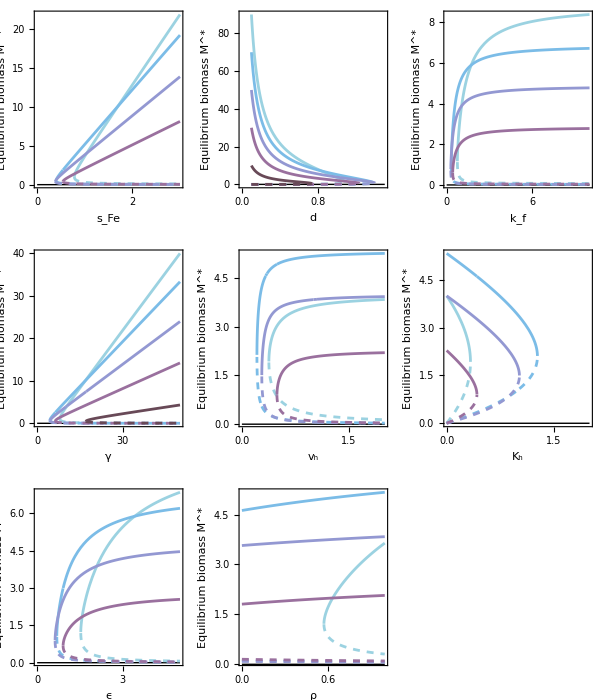

```mathematica
sweepRanges={
(* Chemostat stuff *)
{sFe,0,3,"s_Fe"},
{d,0.1,1.5, "d"},

{kf,0,10, "k_f"},
{γ,0,50, "γ"},
{vh,0,2, "v_h"},
{Kh,0,2,"K_h"},
{ϵ,0,5, "ϵ"},
{ρ,0,1, "ρ"}
};
sweeps=Table[
vals={0.1,0.3,0.5,0.7,0.9};
sweep=Table[Evaluate[M[1]/.(sols/.{α[1]->x, r[[1]]->y}/.defaults)][[2;;3]],{x,vals}];
Plot[sweep,{y,r[[2]],r[[3]]},
Prolog->{Black,Thick,Line[{{r[[2]],0},{r[[3]],0}}]},
PlotStyle->styles,PlotRange->{{0,r[[3]]},All},
Frame->True,FrameLabel->{r[[4]],"Equilibrium biomass M^*"},
PlotTheme->"Default",BaseStyle->Directive[FontColor->Black],
AspectRatio->1.2
(*PlotLegends->SwatchLegend[colors,vals,LegendLabel-> "Value of α_public"]]*)
], {r,sweepRanges}];
GraphicsGrid[Partition[
Append[
sweeps,
SwatchLegend[colors,vals,LegendLabel-> "Value of α"]
],UpTo[3]],ImageSize->{600,700}, AspectRatio->Full]
```

## Allee effect (Figure S1)

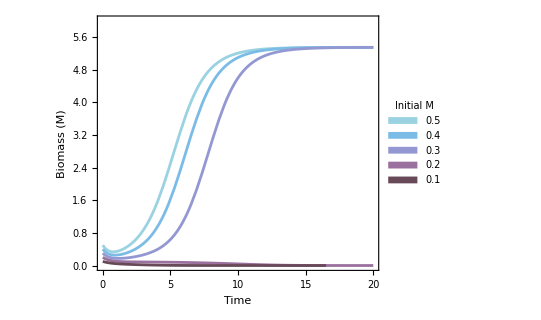

```mathematica
colors=tolIridescent[[{10,13,16,19,22}]];
vals=Reverse[{0.1, 0.2, 0.3,0.4, 0.5}];
sweep=Table[
M[1][t]/.SolvePatch[{0.227},{init},
{apoStart->0,holoStart->0,feStart->sFe}],
{init,vals}];

plt1=Plot[Evaluate[sweep],{t,0,20},
PlotRange->{0,6},
Frame->True,FrameLabel->{"Time","Biomass (M)"},
PlotStyle->colors,
PlotLegends->Placed[SwatchLegend[colors,vals,LegendLabel-> "Initial M"],
{0.85,0.25}],
BaseStyle->Directive[FontColor->Black],
AspectRatio->0.8
]
```

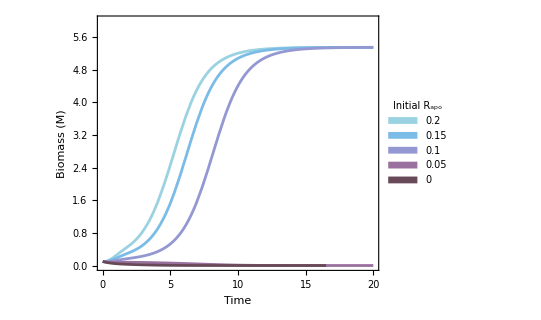

```mathematica
vals=Reverse[{0,0.05, 0.1, 0.15, 0.2}];
sweep=Table[
M[1][t]/.SolvePatch[{0.227},{0.1},
{apoStart->init,holoStart->0,feStart->sFe}],
{init,vals}];

plt2=Plot[Evaluate[sweep],{t,0,20},
PlotRange->{0,6},
Frame->True,FrameLabel->{"Time","Biomass (M)"},
PlotStyle->colors,
PlotLegends->Placed[SwatchLegend[colors,vals,LegendLabel-> "Initial R_apo"],
{0.85,0.25}],
BaseStyle->Directive[FontColor->Black],
AspectRatio->0.8
]
```

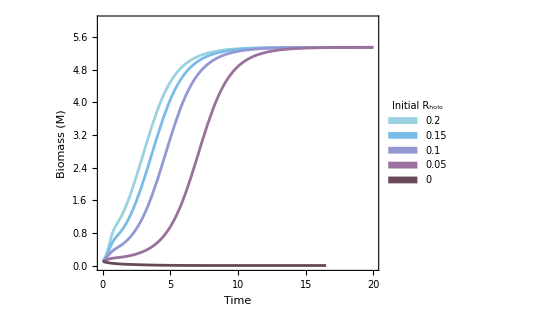

```mathematica
vals=Reverse[{0,0.05, 0.1, 0.15, 0.2}];
sweep=Table[
M[1][t]/.SolvePatch[{0.227},{0.1},
{apoStart->0,holoStart->init,feStart->sFe}],
{init,vals}];

plt3=Plot[Evaluate[sweep],{t,0,20},
PlotRange->{0,6},
Frame->True,FrameLabel->{"Time","Biomass (M)"},
PlotStyle->colors,
PlotLegends->Placed[SwatchLegend[colors,vals,LegendLabel-> "Initial R_holo"],{0.85,0.25}],
BaseStyle->Directive[FontColor->Black],
AspectRatio->0.8
]
```

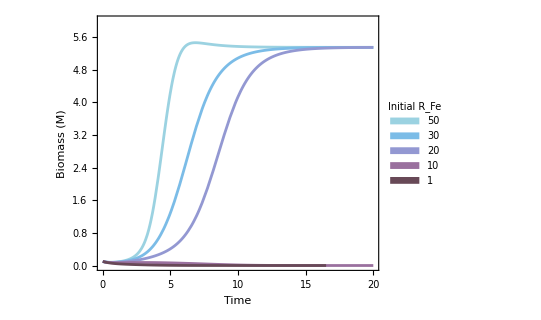

```mathematica
vals=Reverse[{1,10,20, 30, 50}];
sweep=Table[
M[1][t]/.SolvePatch[{0.227},{0.1},
{apoStart->0,holoStart->0,feStart->init}],
{init,vals}];

plt4=Plot[Evaluate[sweep],{t,0,20},
PlotRange->{0,6},
Frame->True,FrameLabel->{"Time","Biomass (M)"},
PlotStyle->colors,
PlotLegends->Placed[SwatchLegend[colors,vals,LegendLabel-> "Initial R_Fe"],{0.85,0.25}],
BaseStyle->Directive[FontColor->Black],
AspectRatio->0.8
]
```

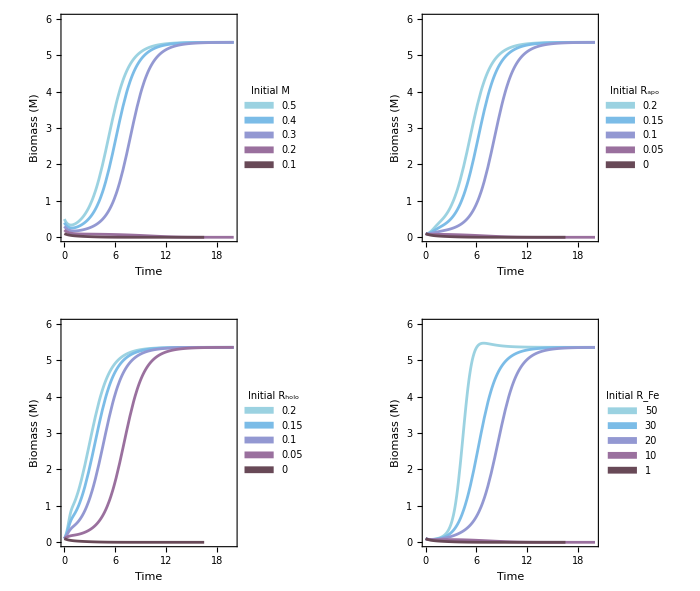

```mathematica
GraphicsGrid[{{plt1,plt2},{plt3,plt4}},ImageSize->700]
```

### Representative dynamics for the kick/flow algorithm parameters (Figure S5)

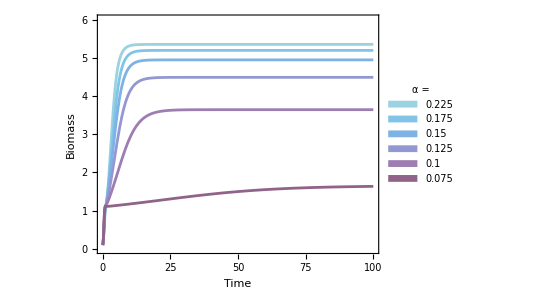

```mathematica
colors=tolIridescent[[{10,12,14,16,18, 20}]];
vals=Reverse[{0.075,0.1, 0.125,0.15,0.175,0.225}];
maxT=100;
sweep=Table[
M[1][t]/.SolvePatch[{alpha},{0.1},
{apoStart->0,holoStart->0.2,feStart->1}, maxT, False],
{alpha,vals}];

plt1=Plot[Evaluate[sweep],{t,0,maxT},
PlotRange->{0,6},
Frame->True,FrameLabel->{"Time","Biomass"},
PlotStyle->colors,
PlotLegends->SwatchLegend[colors,vals,LegendLabel-> "α = "],
BaseStyle->Directive[FontSize->13,FontColor->Black],LabelStyle->Directive[FontColor->Black],
ImageSize->{400,300},
AspectRatio->Full
]
```

```mathematica
colors=tolIridescent[[{10,12,14,16,18, 20}]];
vals=Reverse[{0.075,0.1, 0.125,0.15,0.175,0.225}];
```

```mathematica
sol1=SolvePatch[{0.225},{1},
{apoStart->0,holoStart->0,feStart->1}, 200];
Map[#[sol1["end"]]&,sol1]
```

<|M[1]→5.35123,Apo→2.39324,Holo→0.0148148,Fe→0.294704,end→27.7839[27.7839]|>

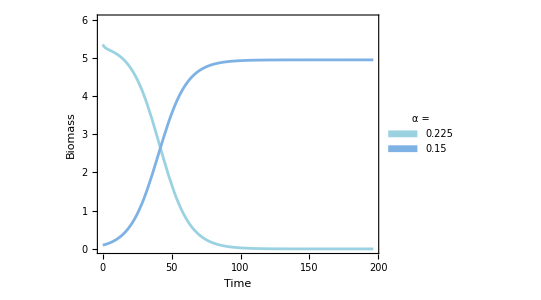

```mathematica
sol2=SolvePatch[{0.225,0.15},{5.35123,0.1},
{apoStart->2.39324,holoStart->0.0148148,feStart->0.294704}, 200];

plt2 =Plot[Evaluate[{M[1][t],M[2][t]}/.sol2],{t,0,Min[sol2["end"],200]},
PlotRange->{0,6},
Frame->True,FrameLabel->{"Time","Biomass"},
PlotLegends->SwatchLegend[tolIridescent[[{10,14}]],{0.225,0.15},LegendLabel-> "α = "],
PlotStyle->tolIridescent[[{10,14}]],
BaseStyle->Directive[FontSize->13,FontColor->Black],LabelStyle->Directive[FontColor->Black],
ImageSize->{400,300},
AspectRatio->Full
]
```

```mathematica
Column[{plt1, plt2}, Left]
```

-Graphics-
-Graphics-